# 20 Gaussian Elimination: LU Decomposition

We know how to solve triangular systems of equations.  We are going to see how to reduce a general system 
	A.x=b 
to two triangular systems.

### Simple Matrices

What does the matrix below do?

```mathematica
L3=IdentityMatrix[8]; L3⟦4;;8,3⟧={L43,L53,L63,L73,L83};
MatrixForm[L3]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | L43 | 1 | 0 | 0 | 0 | 0
0 | 0 | L53 | 0 | 1 | 0 | 0 | 0
0 | 0 | L63 | 0 | 0 | 1 | 0 | 0
0 | 0 | L73 | 0 | 0 | 0 | 1 | 0
0 | 0 | L83 | 0 | 0 | 0 | 0 | 1)

Can you just write down its inverse?

```mathematica
MatrixForm[Inverse[L3]]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | -L43 | 1 | 0 | 0 | 0 | 0
0 | 0 | -L53 | 0 | 1 | 0 | 0 | 0
0 | 0 | -L63 | 0 | 0 | 1 | 0 | 0
0 | 0 | -L73 | 0 | 0 | 0 | 1 | 0
0 | 0 | -L83 | 0 | 0 | 0 | 0 | 1)

### Multiplying Simple Matrices

Here is another “similar” matrix

```mathematica
L4=IdentityMatrix[8]; L4⟦5;;8,4⟧={L54,L64,L74,L84};
MatrixForm[L4]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | L54 | 1 | 0 | 0 | 0
0 | 0 | 0 | L64 | 0 | 1 | 0 | 0
0 | 0 | 0 | L74 | 0 | 0 | 1 | 0
0 | 0 | 0 | L84 | 0 | 0 | 0 | 1)

The product L3.L4 is simple

```mathematica
MatrixForm[L3.L4]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | L43 | 1 | 0 | 0 | 0 | 0
0 | 0 | L53 | L54 | 1 | 0 | 0 | 0
0 | 0 | L63 | L64 | 0 | 1 | 0 | 0
0 | 0 | L73 | L74 | 0 | 0 | 1 | 0
0 | 0 | L83 | L84 | 0 | 0 | 0 | 1)

However, the product L4.L3 is not. To use these matrices we need to work our way down.

```mathematica
MatrixForm[L4.L3]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | L43 | 1 | 0 | 0 | 0 | 0
0 | 0 | L53+L43 L54 | L54 | 1 | 0 | 0 | 0
0 | 0 | L63+L43 L64 | L64 | 0 | 1 | 0 | 0
0 | 0 | L73+L43 L74 | L74 | 0 | 0 | 1 | 0
0 | 0 | L83+L43 L84 | L84 | 0 | 0 | 0 | 1)

### Chaining Simple Matrices

```mathematica
Clear[L]
MatrixForm[
Mat=LowerTriangularize[Table[StringForm["L````",i,j],{i,8},{j,8}],-1]+IdentityMatrix[8]
]
```

The lower triangular matrix below is the product of 7 of these simple matrices.

```mathematica
Clear[L]
MatrixForm[
Mat=LowerTriangularize[Table[StringForm["L````",i,j],{i,8},{j,8}],-1]+IdentityMatrix[8]
]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
L21 | 1 | 0 | 0 | 0 | 0 | 0 | 0
L31 | L32 | 1 | 0 | 0 | 0 | 0 | 0
L41 | L42 | L43 | 1 | 0 | 0 | 0 | 0
L51 | L52 | L53 | L54 | 1 | 0 | 0 | 0
L61 | L62 | L63 | L64 | L65 | 1 | 0 | 0
L71 | L72 | L73 | L74 | L75 | L76 | 1 | 0
L81 | L82 | L83 | L84 | L85 | L86 | L87 | 1)

## Using these Simple Matrices to Create Zeros

### Manually

Gaussian Elimination is the first way people worked out to make zeros. Note, if you were solving equations by candle light in 18XX you would not organize it this way!

```mathematica
m=8;
A0=RandomReal[{-1,1},{m,m}];
L1=IdentityMatrix[m]; L1⟦2;;m,1⟧=A0⟦2;;m,1⟧/A0⟦1,1⟧;
MatrixForm[A1 = Chop[Inverse[L1].A0]]
```

(0.496922 | 0.932058 | -0.724432 | -0.330215 | 0.370034 | -0.68091 | 0.941816 | 0.963368
0 | 1.34402 | -1.0433 | -0.893698 | 0.448953 | -0.6377 | 2.05279 | 1.51479
0 | 1.49542 | -1.5392 | -0.69784 | 0.859483 | -0.717439 | 0.0875724 | 1.22735
0 | -1.45729 | 1.76441 | 0.155937 | -0.415541 | 1.0435 | -0.497015 | -2.28951
0 | -1.20219 | 0.324905 | 1.04513 | -0.510928 | 0.832972 | -1.52519 | -1.95058
0 | -0.0123631 | -0.454243 | 0.244336 | 0.0818151 | -0.729771 | 1.67986 | 0.91035
0 | -0.792088 | 1.13944 | -0.042216 | 0.169166 | -0.0427621 | -0.312306 | -1.42465
0 | -0.431767 | 0.368969 | 0.981574 | 0.291117 | 1.7155 | -1.63723 | -1.4518)

If we do it again we can make another almost column of zeros.

```mathematica
L2=IdentityMatrix[m]; L2⟦3;;m,2⟧=A1⟦3;;m,2⟧/A1⟦2,2⟧;
MatrixForm[A2 = Chop[Inverse[L2].A1]]
```

(0.496922 | 0.932058 | -0.724432 | -0.330215 | 0.370034 | -0.68091 | 0.941816 | 0.963368
0 | 1.34402 | -1.0433 | -0.893698 | 0.448953 | -0.6377 | 2.05279 | 1.51479
0 | 0 | -0.378367 | 0.296534 | 0.359955 | -0.00790184 | -2.19647 | -0.458081
0 | 0 | 0.63318 | -0.813082 | 0.0712497 | 0.352054 | 1.72879 | -0.647058
0 | 0 | -0.608304 | 0.245737 | -0.10935 | 0.262565 | 0.310979 | -0.595635
0 | 0 | -0.46384 | 0.236115 | 0.0859449 | -0.735637 | 1.69874 | 0.924284
0 | 0 | 0.52458 | -0.56891 | 0.433753 | -0.418586 | 0.897492 | -0.531923
0 | 0 | 0.0338076 | 0.694473 | 0.435344 | 1.51064 | -0.977765 | -0.965175)

We can keep going.

```mathematica
L3=IdentityMatrix[m]; L3⟦4;;m,3⟧=A2⟦4;;m,3⟧/A2⟦3,3⟧;
MatrixForm[A3 = Chop[Inverse[L3].A2]]
L4=IdentityMatrix[m]; L4⟦5;;m,4⟧=A3⟦5;;m,4⟧/A3⟦4,4⟧;
MatrixForm[A4 = Chop[Inverse[L4].A3]]
L5=IdentityMatrix[m]; L5⟦6;;m,5⟧=A4⟦6;;m,5⟧/A4⟦5,5⟧;
MatrixForm[A5 = Chop[Inverse[L5].A4]]
L6=IdentityMatrix[m]; L6⟦7;;m,6⟧=A5⟦7;;m,6⟧/A5⟦6,6⟧;
MatrixForm[A6 = Chop[Inverse[L6].A5]]
L7=IdentityMatrix[m]; L7⟦8;;m,7⟧=A6⟦8;;m,7⟧/A6⟦7,7⟧;
MatrixForm[A7 = Chop[Inverse[L7].A6]]
```

(0.496922 | 0.932058 | -0.724432 | -0.330215 | 0.370034 | -0.68091 | 0.941816 | 0.963368
0 | 1.34402 | -1.0433 | -0.893698 | 0.448953 | -0.6377 | 2.05279 | 1.51479
0 | 0 | -0.378367 | 0.296534 | 0.359955 | -0.00790184 | -2.19647 | -0.458081
0 | 0 | 0 | -0.316844 | 0.673619 | 0.33883 | -1.94691 | -1.41364
0 | 0 | 0 | -0.231004 | -0.688053 | 0.275269 | 3.84226 | 0.140826
0 | 0 | 0 | -0.127407 | -0.355324 | -0.72595 | 4.3914 | 1.48585
0 | 0 | 0 | -0.157785 | 0.932807 | -0.429541 | -2.14777 | -1.16702
0 | 0 | 0 | 0.720969 | 0.467506 | 1.50993 | -1.17402 | -1.00611)

(0.496922 | 0.932058 | -0.724432 | -0.330215 | 0.370034 | -0.68091 | 0.941816 | 0.963368
0 | 1.34402 | -1.0433 | -0.893698 | 0.448953 | -0.6377 | 2.05279 | 1.51479
0 | 0 | -0.378367 | 0.296534 | 0.359955 | -0.00790184 | -2.19647 | -0.458081
0 | 0 | 0 | -0.316844 | 0.673619 | 0.33883 | -1.94691 | -1.41364
0 | 0 | 0 | 0 | -1.17917 | 0.0282355 | 5.26171 | 1.17148
0 | 0 | 0 | 0 | -0.626195 | -0.862198 | 5.17428 | 2.05429
0 | 0 | 0 | 0 | 0.597352 | -0.598275 | -1.17823 | -0.463047
0 | 0 | 0 | 0 | 2.0003 | 2.28093 | -5.60416 | -4.22279)

(0.496922 | 0.932058 | -0.724432 | -0.330215 | 0.370034 | -0.68091 | 0.941816 | 0.963368
0 | 1.34402 | -1.0433 | -0.893698 | 0.448953 | -0.6377 | 2.05279 | 1.51479
0 | 0 | -0.378367 | 0.296534 | 0.359955 | -0.00790184 | -2.19647 | -0.458081
0 | 0 | 0 | -0.316844 | 0.673619 | 0.33883 | -1.94691 | -1.41364
0 | 0 | 0 | 0 | -1.17917 | 0.0282355 | 5.26171 | 1.17148
0 | 0 | 0 | 0 | 0 | -0.877192 | 2.38007 | 1.43218
0 | 0 | 0 | 0 | 0 | -0.583971 | 1.48728 | 0.130407
0 | 0 | 0 | 0 | 0 | 2.32883 | 3.32161 | -2.23554)

(0.496922 | 0.932058 | -0.724432 | -0.330215 | 0.370034 | -0.68091 | 0.941816 | 0.963368
0 | 1.34402 | -1.0433 | -0.893698 | 0.448953 | -0.6377 | 2.05279 | 1.51479
0 | 0 | -0.378367 | 0.296534 | 0.359955 | -0.00790184 | -2.19647 | -0.458081
0 | 0 | 0 | -0.316844 | 0.673619 | 0.33883 | -1.94691 | -1.41364
0 | 0 | 0 | 0 | -1.17917 | 0.0282355 | 5.26171 | 1.17148
0 | 0 | 0 | 0 | 0 | -0.877192 | 2.38007 | 1.43218
0 | 0 | 0 | 0 | 0 | 0 | -0.0971946 | -0.823034
0 | 0 | 0 | 0 | 0 | 0 | 9.64037 | 1.5667)

(0.496922 | 0.932058 | -0.724432 | -0.330215 | 0.370034 | -0.68091 | 0.941816 | 0.963368
0 | 1.34402 | -1.0433 | -0.893698 | 0.448953 | -0.6377 | 2.05279 | 1.51479
0 | 0 | -0.378367 | 0.296534 | 0.359955 | -0.00790184 | -2.19647 | -0.458081
0 | 0 | 0 | -0.316844 | 0.673619 | 0.33883 | -1.94691 | -1.41364
0 | 0 | 0 | 0 | -1.17917 | 0.0282355 | 5.26171 | 1.17148
0 | 0 | 0 | 0 | 0 | -0.877192 | 2.38007 | 1.43218
0 | 0 | 0 | 0 | 0 | 0 | -0.0971946 | -0.823034
0 | 0 | 0 | 0 | 0 | 0 | 0 | -80.067)

### Script

All this typing is nuts.  All the L entries can be stored in the same place.  We can recycle the storage for the matrix that winds up being U (the things called A0, A1, …) up above.  Finally, since only a few rows of the matrix are changed at a time changed at a time we might as well do only those rows

4.86593×10^-15

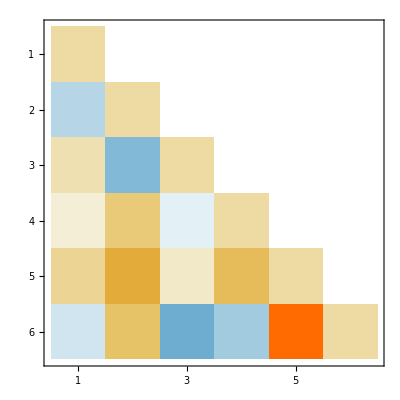
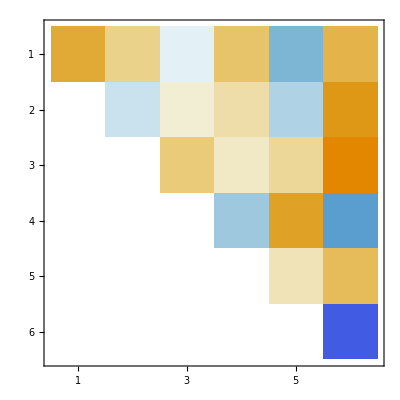

```mathematica
m=6;
A=RandomReal[{-1,1},{m,m}];
(* Start Script *)
L=IdentityMatrix[m];
U=A; 
Do[
Do[
L⟦j,k⟧=U⟦j,k⟧/U⟦k,k⟧;
U⟦j,k;;m⟧-=L⟦j,k⟧ U⟦k,k;;m⟧,
{j,k+1,m}],
{k,1,m-1}]
Norm[A-L.U]
Map[MatrixPlot,{L,U}]
```

### Function

```mathematica
MyLUDecomposition[A_]:= Module[{m=Length[A],L,U=A},
(* Start Script *)
L=IdentityMatrix[m];
Do[
Do[
L⟦j,k⟧=U⟦j,k⟧/U⟦k,k⟧;
U⟦j,k;;m⟧-=L⟦j,k⟧ U⟦k,k;;m⟧,
{j,k+1,m}],
{k,1,m-1}];
{L,U}
]
```

```mathematica
SetOptions[MatrixPlot, PlotLegends->Automatic];
m=1000;
A=RandomReal[{-1,1},{m,m}];
{L,U}=MyLUDecomposition[A];
Norm[A-L.U]
Map[MatrixPlot,{L,U}];
{little,big}=Sort[Abs[Diagonal[U]]]⟦{1,-1}⟧;
big/little
```

2.93348×10^-7

7.73895×10^8

## Solving a Linear System with an LU Decomposition

We know how to solve triangular systems. we even know that the obvious algorithm is backwards stable. We now know how to split a matrix up into two triangular matrices A=L.U.  we should be able to put this together to get an algorithm to solve A.x=L.U.x=b. All we need to do is make up an intermediate variable.  y=U.x 
	L.(U.x)=L.y=b
Solve L.y=b to get a ỹ.  Then solve U.x=ỹ to get x̃.  Since the triangular solves are backwards stable this would all be great if the L.U decomposition was stable!  It is not!

### Need for Pivoting

There are perfectly well behaved linear systems which will break our first attempt at an LU decomposition.  For example
	(ϵ | 1.0
1.0 | 1.0).(x1
x2)=(b1
b2).
In exact arithmetic Gaussian elimination gives the solution
	x1 | = | (b1-b2)/(-1+ϵ) | ⟶ | b2-b1
x2 | = | (-b1+b2 ϵ)/(-1+ϵ) | ⟶ | b1
The system is fine as ϵ→0.  Our first attempt at an LU decomposition gives. 
	A=(ϵ | 1.0
1.0 | 1.0)=(1 | 0
ϵ^-1 | 1)(ϵ | 1.0
0 | 1-ϵ^-1)
which in exact arithmetic works just fine: exact arithmetic does not care that ϵ^-1 could be huge. On any computer this is a real problem!  When ϵ is small in floating point the last entry gets messed up and we will get 
	 (1 | 0
ϵ^-1 | 1)(ϵ | 1.0
0 | -ϵ^-1)=(ϵ | 1
1 | 0)

The sad thing is this has nothing to do with the equations/matrix. As ϵ→0 the condition number κ(A) is the singular value ratio of ratio of (0 | 1.0
1.0 | 1.0) which is roughly 3.

The really sad thing is that if we had just written down the equations in a different order we would have got (1.0 | 1.0
ϵ | 1.0)=(1 | 0
ϵ | 1)(1 | 1
0 | 1-ϵ) which would have worked just fine.

We can not write a usage guide for a function that says “make sure your equations are in a decent order”. We need to make an algorithm that reorders the equations (rows in the matrix) into a good order on the fly.

The first question is given a matrix A which row (same as equation) should we start with.

After the first row we just ask which of the remaining rows is best to do next.

The resulting algorithm is called an LU decomposition with row pivoting.

You can also ask which remaining variable (column of the matrix would be best) which gives column pivoting.

If you ask which is the best variable and equation you are doing complete pivoting!